```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
T1[t_]:=T1[t]=t*IdentityMatrix[1]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.01,1,0]],A:=Inverse[β[ω,0.01,1,0]],B:=Inverse[β[ω,0.01,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[1]-A.T1.Inverse[IdentityMatrix[1]-B.T2.J.T2].B.T1].A,4000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]]
```

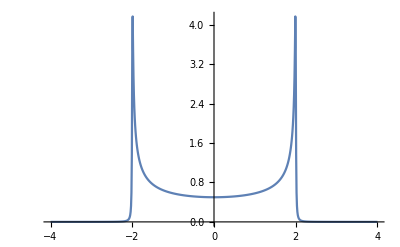

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0][[1,1]]]},{ω,Range[-4,4,0.01]}],PlotRange->All]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:= Inverse[(ω+ⅈ*δ-ϵ1)IdentityMatrix[1]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,m_,n_,o_,p_,q_]:=Module[{gg=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1],imp=imp[ω,δ,t,ϵ,ϵ1]},sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,n]; J=J];sl2=Inverse[IdentityMatrix[1]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,m]; J=J];sl4=Inverse[IdentityMatrix[1]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,o]; J=J];sl6=Inverse[IdentityMatrix[1]-imp.T.sl5.T].imp; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,p]; J=J];sl8=Inverse[IdentityMatrix[1]-imp.T.sl7.T].imp; sl9=Module[{J=sl8},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,q]; J=J];Il1:=Inverse[IdentityMatrix[1]-sl9.T1[1].SR[ω,0.001,1,0].T1[1]].sl9;
Ir1:=Inverse[IdentityMatrix[1]-SR[ω,δ,1,0].T1[1].sl9.T1[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
RandomInteger[{0,20}]
```

16

```mathematica
Mean[Table[tr1[0.1,0.01,1,0,1,RandomInteger[{0,20}],RandomInteger[{0,20}],RandomInteger[{0,20}],RandomInteger[{0,20}],RandomInteger[{0,20}]],10000]]
```

0.693958

```mathematica
f[ϵ1_]:=Table[{ω,Mean[Table[tr1[ω,0.01,1,0,ϵ1,RandomInteger[{0,20}],RandomInteger[{0,20}],RandomInteger[{0,20}],RandomInteger[{0,20}],RandomInteger[{0,20}]],10000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
Export["1d4imp1.csv",f[1]]
```

1d4imp1.csv

```mathematica
Export["1d4imp3.csv",f[0.3]]
```

1d4imp3.csv

```mathematica
Export["1d4imp4.csv",f[0.4]]
```

1d4imp4.csv

```mathematica
Export["1d4imp5.csv",f[0.5]]
```

1d4imp5.csv

```mathematica
Export["1d4imp6.csv",f[0.6]]
```

1d4imp6.csv

```mathematica
Export["1d4imp7.csv",f[0.7]]
```

1d4imp7.csv

```mathematica
Export["1d4imp8.csv",f[0.8]]
```

1d4imp8.csv

```mathematica
Export["1d4imp9.csv",f[0.9]]
```

1d4imp9.csv

```mathematica
Import["1d4imp9.csv"]
```

{{0.,0.710507},{0.01,0.715983},{0.02,0.719212},{0.03,0.725611},{0.04,0.734128},{0.05,0.744414},{0.06,0.745099},{0.07,0.744853},{0.08,0.739509},{0.09,0.730975},{0.1,0.726175},{0.11,0.721142},{0.12,0.716821},{0.13,0.708143},{0.14,0.707427},{0.15,0.705627},{0.16,0.705397},{0.17,0.707049},{0.18,0.703843},{0.19,0.708438},{0.2,0.709909},{0.21,0.711519},{0.22,0.71706},{0.23,0.713113},{0.24,0.712613},{0.25,0.708043},{0.26,0.710054},{0.27,0.71035},{0.28,0.708944},{0.29,0.711305},{0.3,0.715124},{0.31,0.712959},{0.32,0.713616},{0.33,0.711707},{0.34,0.71623},{0.35,0.715003},{0.36,0.71811},{0.37,0.713817},{0.38,0.713876},{0.39,0.71207},{0.4,0.707662},{0.41,0.704452},{0.42,0.703826},{0.43,0.700036},{0.44,0.700557},{0.45,0.699495},{0.46,0.699332},{0.47,0.70081},{0.48,0.69939},{0.49,0.697545},{0.5,0.701807},{0.51,0.701393},{0.52,0.70076},{0.53,0.701549},{0.54,0.705088},{0.55,0.706542},{0.56,0.705053},{0.57,0.708216},{0.58,0.70878},{0.59,0.709656},{0.6,0.70998},{0.61,0.708474},{0.62,0.708473},{0.63,0.710032},{0.64,0.709981},{0.65,0.70734},{0.66,0.706698},{0.67,0.70488},{0.68,0.700983},{0.69,0.700893},{0.7,0.695222},{0.71,0.698451},{0.72,0.693153},{0.73,0.691594},{0.74,0.691225},{0.75,0.689524},{0.76,0.687503},{0.77,0.691101},{0.78,0.690056},{0.79,0.693472},{0.8,0.69339},{0.81,0.694511},{0.82,0.691692},{0.83,0.692988},{0.84,0.694348},{0.85,0.696097},{0.86,0.695083},{0.87,0.697185},{0.88,0.699501},{0.89,0.699673},{0.9,0.701097},{0.91,0.69686},{0.92,0.69377},{0.93,0.692789},{0.94,0.691572},{0.95,0.690415},{0.96,0.689401},{0.97,0.687539},{0.98,0.690771},{0.99,0.687868},{1.,0.686307},{1.01,0.683614},{1.02,0.67892},{1.03,0.676044},{1.04,0.676882},{1.05,0.677028},{1.06,0.678387},{1.07,0.679866},{1.08,0.683674},{1.09,0.677601},{1.1,0.681723},{1.11,0.685582},{1.12,0.681871},{1.13,0.681093},{1.14,0.682396},{1.15,0.684246},{1.16,0.685162},{1.17,0.67999},{1.18,0.678519},{1.19,0.674551},{1.2,0.674128},{1.21,0.66799},{1.22,0.665285},{1.23,0.661014},{1.24,0.660881},{1.25,0.664711},{1.26,0.65829},{1.27,0.658512},{1.28,0.658556},{1.29,0.656633},{1.3,0.658879},{1.31,0.659238},{1.32,0.662854},{1.33,0.662601},{1.34,0.665356},{1.35,0.664682},{1.36,0.663084},{1.37,0.666133},{1.38,0.666359},{1.39,0.667129},{1.4,0.663318},{1.41,0.661515},{1.42,0.654426},{1.43,0.646573},{1.44,0.642063},{1.45,0.641151},{1.46,0.636604},{1.47,0.635122},{1.48,0.634226},{1.49,0.631339},{1.5,0.638459},{1.51,0.635501},{1.52,0.636798},{1.53,0.637145},{1.54,0.640028},{1.55,0.640154},{1.56,0.642901},{1.57,0.641383},{1.58,0.643637},{1.59,0.641436},{1.6,0.635055},{1.61,0.633041},{1.62,0.622484},{1.63,0.616015},{1.64,0.614042},{1.65,0.612846},{1.66,0.604927},{1.67,0.60563},{1.68,0.607468},{1.69,0.607449},{1.7,0.609661},{1.71,0.612259},{1.72,0.6113},{1.73,0.611434},{1.74,0.608877},{1.75,0.613619},{1.76,0.605459},{1.77,0.600272},{1.78,0.585944},{1.79,0.579186},{1.8,0.568146},{1.81,0.566504},{1.82,0.560379},{1.83,0.550308},{1.84,0.549771},{1.85,0.546},{1.86,0.543173},{1.87,0.544777},{1.88,0.53854},{1.89,0.526365},{1.9,0.509863},{1.91,0.49201},{1.92,0.464989},{1.93,0.448847},{1.94,0.45441},{1.95,0.510973},{1.96,0.607017},{1.97,0.744632},{1.98,1.01897},{1.99,1.51291},{2.,0.272851},{2.01,0.273176},{2.02,0.113691},{2.03,0.0710754},{2.04,0.15205},{2.05,0.0309577},{2.06,0.0625561},{2.07,0.013482},{2.08,0.0190235},{2.09,0.0439157},{2.1,0.223676},{2.11,0.0781019},{2.12,0.0289596},{2.13,0.0916},{2.14,0.323347},{2.15,0.122849},{2.16,0.288659},{2.17,0.515133},{2.18,0.885626},{2.19,11.6766},{2.2,2.78618},{2.21,0.600387},{2.22,0.249038},{2.23,0.190798},{2.24,0.0475677},{2.25,0.0998488},{2.26,0.0274455},{2.27,0.0202167},{2.28,0.102911},{2.29,0.0128815},{2.3,0.00707966},{2.31,0.0147053},{2.32,0.0144688},{2.33,0.191179},{2.34,0.00985337},{2.35,0.00703578},{2.36,0.00292494},{2.37,0.0015684},{2.38,0.00105648},{2.39,0.00190496},{2.4,0.00396352},{2.41,0.0106326},{2.42,0.066604},{2.43,0.240173},{2.44,0.0192305},{2.45,0.00836022},{2.46,0.00287028},{2.47,0.00108698},{2.48,0.000915312},{2.49,0.000500133},{2.5,0.000483955},{2.51,0.000353031},{2.52,0.00016327},{2.53,0.000153503},{2.54,0.000122728},{2.55,0.000201267},{2.56,0.000201362},{2.57,0.000126824},{2.58,0.0000773686},{2.59,0.000508327},{2.6,0.0000705423},{2.61,0.0000790263},{2.62,0.0000639477},{2.63,0.0000689505},{2.64,0.0000609466},{2.65,0.0000556319},{2.66,0.0000512214},{2.67,0.0000490397},{2.68,0.0000775765},{2.69,0.0000446313},{2.7,0.0000422428},{2.71,0.0000410233},{2.72,0.0000397159},{2.73,0.0000375625},{2.74,0.0000365313},{2.75,0.0000349586},{2.76,0.0000337573},{2.77,0.0000328722},{2.78,0.0000315341},{2.79,0.0000303},{2.8,0.000029479},{2.81,0.0000287891},{2.82,0.0000277157},{2.83,0.0000265861},{2.84,0.0000257865},{2.85,0.0000250653},{2.86,0.0000241705},{2.87,0.000023546},{2.88,0.000022545},{2.89,0.0000224252},{2.9,0.0000215693},{2.91,0.0000210037},{2.92,0.0000204468},{2.93,0.0000198539},{2.94,0.000019278},{2.95,0.0000186979},{2.96,0.0000182833},{2.97,0.0000176737},{2.98,0.0000173562},{2.99,0.0000169619},{3.,0.0000164786}}

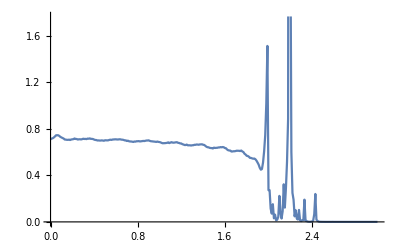

```mathematica
ListPlot[%420,Joined->True]
```

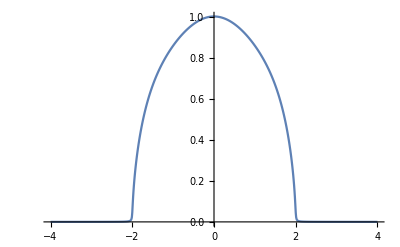

```mathematica
ListLinePlot[Table[{ω,-Im[sl1[ω,0.001,1,0,2][[1,1]]]},{ω,Range[-4,4,0.01]}],PlotRange->All]
```